# Run uniaxialintegratorV1.wl

## Call integrator

```mathematica
SetDirectory[NotebookDirectory[]];
<<uniaxialintegratorV2`
```

# Original

## 3 target surfaces Reproduce fig 1

## Inverse problem set up

Give material and surface properties

Designable features:

```mathematica
ϵ={ϵ1};
```

Deformation magnitude along and across the director:

```mathematica
λ1[epsilon_,lambda_]:=1
λ2[epsilon_,lambda_]:=Exp[lambda epsilon[[1]]];
```

Actuation values of the stimuli:

```mathematica
Λ={0,1,2};
```

Target geometries:

```mathematica
g1=DiagonalMatrix[{1,1}]&;
g2={{1,0},{0,Sin[#[[1]]]^2}}&;
g3=embeddingToMetric[{x,y,Exp[-(x^2+y^2/4)]},{x,y}]@@#&;
gList={g1,g2,g3}
```

{DiagonalMatrix[{1,1}]&,{{1,0},{0,Sin[#1⟦1⟧]^2}}&,embeddingToMetric[{x,y,Exp[-(x^2+y^2/4)]},{x,y}]@@#1&}

g2 and g3 are  derived in this example for a sphere and an anisotropic gaussian 
rrg[x_,y_]={x,y,Exp[-x^2/1-y^2/4]}, respectively.

We then verify that the problem is hyperbolic, and can be substantially solved from initial data :

```mathematica
CheckSolverValidity[λ1,λ2,ϵ,Λ]
```

Go ahead

ϵ1 and p1initial conditions along v

Finally, we derive the propagation equations for the inverse design of the sheet:

```mathematica
propagation=propagationInverseEqns[{g1,g2,g3},λ1,λ2,ϵ,Λ];
```

and calculate where to assign the initial data for ϵ, along the initial u-curve or v-curve:

```mathematica
i12assignment=i12assign[λ1,λ2,ϵ,Λ]
```

{2}

## Give initial conditions

Initial u and v curves, specified parametrically on the initial surface:

```mathematica
ucurve[t_]=t{1,0};
vcurve[t_]=2{1-Cos[t],Sin[t]};
```

Initial positions and directors on the target surfaces:

```mathematica
initialpositions={ucurve[0],{Pi/2,0},{0,0}};
initialdirectors=MapThread[normalizevec[#1,#2[#3]]&,{{D[ucurve[t],t]/.t->0,{1,0},{1,0}},{g1,g2,g3},initialpositions}]
```

{{1,0},{1,0},{1,0}}

Initial values of the designable features ϵ, and their derivatives p and q, given as parametric functions:

```mathematica
epsinitial[t_]={1/2};
pqinitial[t_]={1/2};
```

which are now collected

```mathematica
initialconditions={initialpositions,initialdirectors,epsinitial[t],pqinitial[t],ucurve[t],vcurve[t],gList[[1]],i12assignment};
```

We then test the initial conditions to verify that they are well posed at the origin:

```mathematica
testInitialData[propagation,initialconditions]
```

Propagation Equations and data at the origin are numeric

True

## Diagonal integrate

The inverse design problem is then integrated to obtain the fabrication data.
The data structure = Table[ {uv, r, n, α, β, ϵ, b, s, p, q},  {u,umax[[v]]}, {v,vmax}, {quad,4}]
Where quad - stands for the Cartesian quadrant.
u, and v are enumerated u and v curves.
uv={u-value,v-value};
r={{x1,y1},{x2,y2},...,{xm,ym}} = A list of 2d coordinates on the initial and target surfaces.
n={{n1x,n1y},{n2x,n2y},...,{nmx,nmy}} = A list of images of the director on the initial and target surfaces.
α = arclength along u on the initial sheet.
β = arclength along v on the initial sheet.
ϵ= {ϵ1,ϵ2,...,ϵ_(m-1)} = list of designable features 
b= bend of director field
s= splay of director field
p={p1,p2,...,p_(m-1)} = list of variations of ϵ along u.
q={q1,q2,...,q_(m-1)} = list of variations of ϵ along v.

We now integrate the inverse problem with the following mesh setup:
maxdiag = maximal number of integration steps along each direction.
du  = step size along u,
dv =stepsize  along v, 
signu (signv)  = increase or decrease u (v);

```mathematica
intDiag[maxdiag_,signu_,signv_,du_,dv_]:=diagonalintegration[ucurve[t],vcurve[t],initialpositions,initialdirectors,epsinitial[t],pqinitial[t],λ1,λ2,Λ,gList,propagation,i12assignment,maxdiag,du,signu,dv,signv];
```

Build dataset:

```mathematica
ClearAll@@Table["data"<>ToString[i],{i,4}];
ClearAll[result]
ClearAll@@Table["vmax"<>ToString[i],{i,4}];
ClearAll@@Table["umaxtab"<>ToString[i],{i,4}];
datas=stringlist["data",4];
umaxtabs=stringlist["umaxtab",4];
vmaxs=stringlist["vmax",4];
quads={{1,1},{-1,1},{-1,-1},{1,-1}};
```

Integrate

```mathematica
maxdiag=200;
du=1/20;
dv=1/20;
(result=ParallelTable[intDiag[maxdiag,q[[1]],q[[2]],du,dv],{q,quads}];)//AbsoluteTiming
MapThread[Set[{#1,#2,#3},result[[#4]]]&,{umaxtabs,vmaxs,datas,Range[4]}];
```

ustop at {21, 1}

ustop at {21, 1}

ustop at {31, 1}

ustop at {31, 1}

{49.8067,Null}

## Plot Integrated Designable Elastic Features:

The director pattern to be fabricated is then:

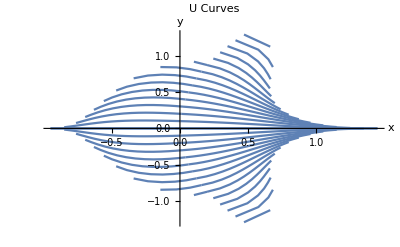

```mathematica
Show[Table[Table[ListLinePlot[datas[[quad,;;umaxtabs[[quad,vv]],vv,2,1]]],{vv,1,vmaxs[[quad,1]],2}],{quad,4}],PlotRange->All,PlotLabel->"U Curves",AxesLabel->{"x","y"}]
```

The designable features ϵ_1 and ϵ_2 to be fabricated are:

```mathematica
ListPointPlot3D[Join[#1,{#2}]&@@@Flatten[Table[Table[{#[[1,1]],#[[2,1]]}&/@datas[[quad,;;umaxtabs[[quad,vv]],vv,{2,6}]],{vv,vmaxs[[quad,1]]}],{quad,4}],2],PlotRange->All,PlotLabel->"Designable feature ϵ_1",AxesLabel->{"x","y","ϵ_1"}]
```

-Graphics3D-

## Resulting 3D surfaces

The actuated surfaces then take the shapes:

```mathematica
fig3p1=Show[tubeEmbedColor[datas[[#]],umaxtabs[[#]],vmaxs[[#,1]],1,1,1,1,{x,y,0},{x,y}]&/@Range[4]]
fig3p2=Show[tubeEmbedColor[datas[[#]],umaxtabs[[#]],vmaxs[[#,1]],1,1,1,2,10RotationMatrix[-Pi/2,{0,1,0}].{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,ϕ}]&/@Range[4]]
fig3p3=Show[tubeEmbedColor[datas[[#]],umaxtabs[[#]],vmaxs[[#,1]],1,1,1,3,{x,y,Exp[-(x^2+y^2/4)]},{x,y}]&/@Range[4]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-